# Restavracije z Michelinovimi zvezdicami

## Opis in ideja teme

Sam se dokaj zanimam o restavracijah, torej je bila logična odločitev, da poskusim analizirati nekaj o njih. Logično se je zdelo, da za analizo uporabim “Svetovni standard” - Michelinove zvezdice. Predstavil bom nekaj različnih grafov in dodal zemljevid vseh restavracij.

## Uvoz podatkov iz Kaggla

Najprej sem seveda uvozil podatke, nekateri so bolj uporabni, nekateri pa manj, torej jih malo počistimo.

```mathematica
data = Import[NotebookDirectory[]<>"michelin_my_maps2.csv", "Table", FieldSeparators -> ",", HeaderLines -> 1, CharacterEncoding -> "UTF8"]//Prepend[#,{"Ime", "Naslov", "Lokacija", "MinCena", "MaxCena", "Valuta", "Tip kuhinje", "GeoŠirina", "GeoDolžina", "Telefon", "URL", "Naslov strani", "Nagrada"} ]& //ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

## Čiščenje podatkov

Nekaj vrstic je, ki so popolnoma neuporabne, nekatere so pa čudno formatirane - pa jih popravimo.

```mathematica
precisceni = data // 
Query[All,<|"Ime" -> "Ime", "Naslov" -> "Naslov", "Lokacija" -> "Lokacija", "MinCena" ->"MinCena", "MaxCena" -> "MaxCena", "Valuta" -> "Valuta", "Tip kuhinje" ->"Tip kuhinje", "GeoŠirina"->"GeoŠirina", "GeoDolžina"->"GeoDolžina", "Nagrada"->"Nagrada"|>]//
Query[All, <|  #,"MinCena" -> If[#MinCena == "-", 0, #MinCena] |>&]//
Query[Select[#MinCena > 0&],All]//
Query[All, <|  #,"Nagrada" -> If[#Nagrada == "-", 0, #Nagrada] |>&]//
Query[Select[#Nagrada != 0&],All]
```

Dataset[<>]

```mathematica
pr = precisceni // Query[All, <|  #,"MinCena" -> If[#Valuta == "EUR", #MinCena, CurrencyConvert[Quantity[#MinCena,#Valuta],"EUR"]] |>&]
```

Failure[…]

Sedaj smo malo prečistili vse, edino kar ni uspelo je sprememba vseh valut v EUR.

## Analiza podatkov

Z lepšo tabelo lahko sedaj vizualiziramo podatke. Pogledali bomo: razmerja med številom 1- 2- in 3- michelinskimi restavracijami, količino zvezdic na valuto,  kakšni tipi kuhinje so, na koncu bo pa še vizualizacija vseh lokacij.

## Razmerje med številom 1-, 2-, in 3-Michelinskih restavracij

```mathematica
analiza1 = precisceni //Query[All,<|"Ime" -> "Ime",  "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy[#Nagrada&]]
```

Dataset[<>]

```mathematica
analiza1v2 = precisceni[GroupBy["Nagrada"],Join,"Ime"]
```

```mathematica
PieChart[<|"3 Michelinke"->130,"2 Michelinki"->440,"1 Michelinka"->2391|>,ChartStyle->66, ChartLabels->Automatic]
```

-Graphics-

## Zvezdice na valuto(regijo)

```mathematica
analiza2 =precisceni //Query[All,<|"Ime" -> "Ime", "Valuta" -> "Valuta", "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy["Valuta"]]
```

Dataset[<>]

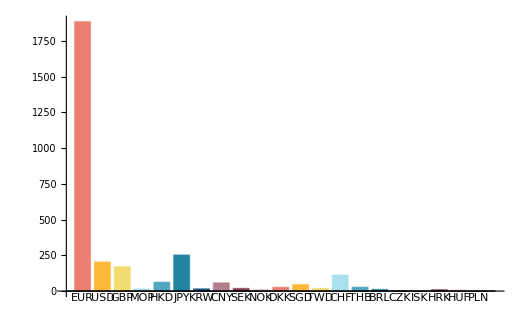

```mathematica
BarChart[<|"EUR"->1886,"USD"->204,"GBP"->171,"MOP"->15,"HKD"->63,"JPY"->253, "KRW"->16, "CNY" ->58, "SEK" ->19, "NOK"->10, "DKK"->27, "SGD"->46,"TWD"->19, "CHF"->113, "THB"->28, "BRL"->12, "CZK"->2, "ISK"->3, "HRK"->10, "HUF"->7, "PLN"->3|>,ChartStyle->24, ChartLabels->Automatic]
```

## Tipi kuhinje

```mathematica
analiza3 =precisceni //Query[All,<|"Ime" -> "Ime", "Tip kuhinje" -> "Tip kuhinje", "Nagrada"->"Nagrada"|>]// 
Query[Select[#Nagrada != "Bib Gourmand"&],All]//
Query[GroupBy["Tip kuhinje"]]
```

Dataset[<>]

## Geografska analiza

Da se ne ukvarjamo s tisočimi točkami na mapi, izberemo samo 3-michelinske restavracije.

```mathematica
smaller= precisceni//
Query[Select[#Nagrada == "3 MICHELIN Stars"&],All]
```

```mathematica
tromich = smaller[All, "Lokacija"]//Normal
```

{Kruiningen,Zwolle,Kruishoutem,Roeselare,Antwerpen,Washington,Chicago,Paris,Paris,Paris,Paris,Paris,Paris,La Rochelle,Valence,Paris,Chagny,Paris,Megève,Annecy,Les Baux-de-Provence,Saint-Tropez,Ouches,Le Castellet,Reims,Cassis,Courchevel,Vonnas,Saint-Bonnet-le-Froid,Marseille,Menton,Fontjoncouse,Monaco,Paris,Paris,Saint-Martin-de-Belleville,Marseille,Eugénie-les-Bains,Wolfsburg,Hamburg,Rottach-Egern,Perl,Berlin,Baiersbronn,Baiersbronn,Piesport,Dreis,Cartmel,Bray,Bray,London,London,London,London,London,Vienna,Macau,Macau,Macau,Hong Kong,Hong Kong,Hong Kong,Hong Kong,Hong Kong,Hong Kong,Hong Kong,Larrabetzu,Lasarte - Oria,El Puerto de Santa María,Girona,Dénia,Villaverde de Pontones,Madrid,Donostia / San Sebastián,Donostia / San Sebastián,Barcelona,Barcelona,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,Tokyo,SEOUL,SEOUL,Runate,Rubano,Castel di Sangro,Modena,Brusaporto,San Cassiano,Milan,Florence,Alba,Senigallia,Rome,Shanghai,Osaka,Osaka,Kyoto,Kyoto,Kyoto,Kyoto,Kyoto,Yountville,Healdsburg,Los Gatos,San Francisco,San Francisco,San Francisco,Stockholm,Oslo,Copenhagen,Copenhagen,Singapore,Singapore,Singapore,Taipei,New York,New York,New York,New York,New York,Crissier,Basel,Fürstenau}

Tukaj zmanjšamo velikost seznama, saj mathematica začne kolcat.

```mathematica
Func[a_]:=Interpreter["City"][ a]
```

```mathematica
supersmall = tromich [[1;;20]]
```

{Kruiningen,Zwolle,Kruishoutem,Roeselare,Antwerpen,Washington,Chicago,Paris,Paris,Paris,Paris,Paris,Paris,La Rochelle,Valence,Paris,Chagny,Paris,Megève,Annecy}

```mathematica
entities = Map[Func, supersmall]
```

{Failure[…],Zwolle,Kruishoutem,Roeselare,Antwerp,Washington,Chicago,Paris,Paris,Paris,Paris,Paris,Paris,La Rochelle,Valence,Paris,Chagny,Paris,Megève,Annecy}

```mathematica
GeoListPlot[entities]
```

-Graphics-